Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
Clear["Global`*"]
```

1 - 10 Sample Regression Line
Find and graph the sample regression line of y on x and the given data as points on the same axes.

1.  (0, 1.0), (2, 2.1), (4, 2.9), (6, 3.6), (8, 5.2)

```mathematica
dat={{0,1.0},{2, 2.2},{4,2.9},{6,3.6},{8,5.2}}
```

{{0,1.},{2,2.2},{4,2.9},{6,3.6},{8,5.2}}

```mathematica
Fit[dat,{1,x},x]
```

1.02+0.49 x

The fitting line found by the text answer is 0.98+0.495 x. As shown in the plot below, there is not a great difference between Mathematica's line and the text’s.

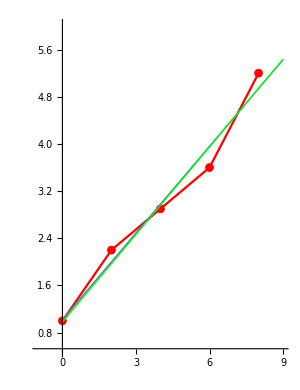

```mathematica
pch=ListLinePlot[dat,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->Red,PlotRange->{{-1,9},{0.5,6}},Epilog->{{RGBColor[0.4,0.4,0.9],Line[{{0,1.02},{9,1.02+0.49*9}}]},{{Green,Line[{{0,0.98},{9,0.98+0.495*9}}]}}}]
```

3.  x = Revolutions per minute, y = Power of a diesel engine (hp)

x | 400 | 500 | 600 | 700 | 750
y | 5800 | 10300 | 14200 | 18800 | 21000

```mathematica
rdat={{400,5800},{500,10300},{600,14200},{700,18800},{750,21000}}
```

{{400,5800},{500,10300},{600,14200},{700,18800},{750,21000}}

```mathematica
Fit[rdat,{1,x},x]
```

-11457.9+43.1829 x

The above equation in green matches the answer in the text.

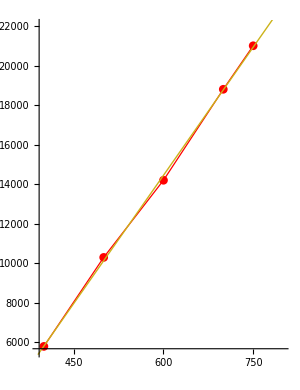

```mathematica
rch=ListLinePlot[rdat,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->{Red,Thickness[0.003]},PlotRange->{{390,800},{5600,22000}},Epilog->{{RGBColor[0.8,0.7,0.1],Line[{{390,-11457.9+43.182 *390},{800,-11457.9+43.182*800}}]}}]
```

5.  x = Brinell hardness, y = Tensile strength (in 1000 psi) of steel with 0.45% C tempered for 1 hour.

x | 200 | 300 | 400 | 500
y | 110 | 150 | 190 | 280

```mathematica
brin={{200,110},{300,150},{400,190},{500,280}}
```

{{200,110},{300,150},{400,190},{500,280}}

```mathematica
Fit[brin,{1,x},x]
```

-10.+0.55 x

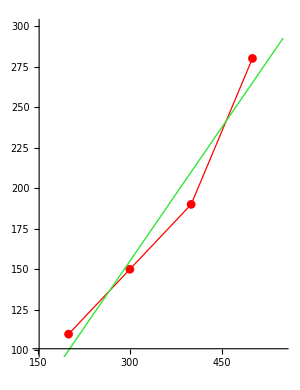

```mathematica
bch=ListLinePlot[brin,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->{Red,Thickness[0.003]},PlotRange->{{150,550},{100,300}},Epilog->{{RGBColor[0.2,0.9,0.2],Line[{{150,-10.0+0.55 *150},{550,-10.0+0.55*550}}]}}]
```

7. Ohm’s law (section 2.9). x = Voltage (V), y = current (A). Also find the resistance R (Ω).

x | 40 | 40 | 80 | 80 | 110 | 110
y | 5.1 | 4.8 | 0.0 | 10.3 | 13.0 | 12.7

```mathematica
volt={{40,5.1},{40,4.8},{80,10.3},{110,13.0},{110,12.7}}
```

{{40,5.1},{40,4.8},{80,10.3},{110,13.},{110,12.7}}

First I drop the point that represents zero current. Afterwards the fitting line of Mathematica (green) is almost the same as that of the text answer (blue).

```mathematica
Fit[volt,{1,x},x]
```

0.55122+0.113537 x

```mathematica
model=LinearModelFit[volt,x,x]
```

FittedModel[-0.555405+0.107027 x]

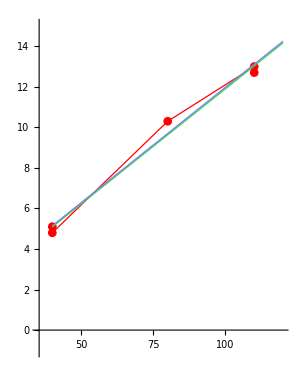

```mathematica
vch=ListLinePlot[volt,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->{Red,Thickness[0.003]},PlotRange->{{35,120},{-1,15}},Epilog->{{RGBColor[0.2,0.9,0.2],Line[{{40,0.5512+0.1135*40},{120,0.5512+0.1135*120}}]},{RGBColor[0.5,0.5,1],Line[{{40,0.5932+0.1138*40},{120,0.5932+0.1138*120}}]}}]
```

The resistance is mysterious. Sum of volts divided by sum of amps does not do it, not quite. Instead, the resistance is equal to the reciprocal of the line slope.

```mathematica
vt=160+220
```

380

```mathematica
at=9.9+23.3+12.7
```

45.9

```mathematica
380/45.9
```

8.27887

```mathematica
1/0.1137
```

8.79507

9. Thermal conductivity of water. x = temperature (deg-F), y = conductivity (Btu/(hr × ft × deg-F). Also find y at room temperature 66 deg-F.

x | 32 | 50 | 100 | 150 | 212
y | 0.337 | 0.345 | 0.365 | 0.380 | 0.395

```mathematica
wat={{32,0.337},{50,0.345},{100,0.365},{150,0.380},{212,0.395}}
```

{{32,0.337},{50,0.345},{100,0.365},{150,0.38},{212,0.395}}

```mathematica
Fit[wat,{1,x},x]
```

0.329232+0.000323239 x

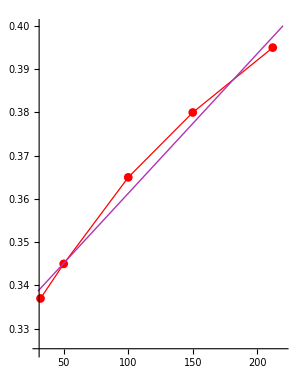

```mathematica
wch=ListLinePlot[wat,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->{Red,Thickness[0.003]},PlotRange->{{30,220},{0.325,0.4}},Epilog->{{RGBColor[0.7,0.2,0.7],Line[{{30,0.329+0.000323*30},{220,0.329+0.000323*220}}]}}]
```

```mathematica
0.3292+0.000323 66
```

0.350518

I cannot find the right chop for the above expression to get the exact text answer decimals, which show as 0.35035.

12 - 15 Confidence intervals
Find a 95% confidence interval for the regression coefficient κ_1 , assuming (A2) and (A3) hold and using the sample.

13. In problem 3.

I gained some info on regression coefficients from https : // mathematica.stackexchange.com/questions/19608/obtaining - standardised - regression - coefficients. The keyword is ‘standardised’. The text answer does not care about standardized regression coefficients, which it seems are based on units of standard deviation. Regular non-standardized ones seem to simply be based on x length, and it is those I am after.

```mathematica
rdat={{400,5800},{500,10300},{600,14200},{700,18800},{750,21000}}
```

{{400,5800},{500,10300},{600,14200},{700,18800},{750,21000}}

Getting the model seems to go okay.

```mathematica
model=LinearModelFit[rdat,x,x]
```

FittedModel[-11457.9+43.1829 x]

I try to use the method which the o.p. said he was using at the time of his post, which he considered to be only an estimate. I should say that in the docs for LinearModelFit it says that the default confidence level is .95, the same as requested in the problem description. (Raising the confidence level to .99 in the command does not change the output table values.) The text answer for the regression coefficient is 41.7 ≤ κ_1 ≤ 44.7. The estimate for x in the below table is right in the middle of that interval. Adding and subtracting the Standard Error still results in an interval shorter than the one in the text answer. This seems to satisfy the current requirement.

```mathematica
model["ParameterTable",ConfidenceLevel->.95]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | -11457.9 | 379.612 | -30.1833 | 0.0000798837
x | 43.1829 | 0.628769 | 68.6786 | 6.80261×10^-6

```mathematica
43.1829+0.628769
```

43.8117

```mathematica
43.1829-0.628769
```

42.5541

15. x = Humidity of air (%), y = Expansion of gelatin (%),

x | 10 | 20 | 30 | 40
y | 0.8 | 1.6 | 2.3 | 2.8

```mathematica
Clear[model]
```

```mathematica
air={{10,0.8},{20,1.6},{30,2.3},{40,2.8}}
```

{{10,0.8},{20,1.6},{30,2.3},{40,2.8}}

```mathematica
model=LinearModelFit[air,x,x]
```

FittedModel[0.2+0.067 x]

Again the displayed regression coefficient is in the center of the text answer, which is 0.046 ≤ κ_1 ≤ 0.088. Again adding and subtracting the Standard Error results in a shorter interval than shown in the text answer.

```mathematica
model["ParameterTable",ConfidenceLevel->.95]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.2 | 0.131339 | 1.52277 | 0.267257
x | 0.067 | 0.00479583 | 13.9705 | 0.00508459

```mathematica
0.067+0.00479583
```

0.0717958

```mathematica
0.067-0.00479583
```

0.0622042

Again I will assume I found what I was looking for.